# Tips & Tricks: Mathematica for Research

## Lecture 3 (17/04/2026)

```mathematica
Quit[]
```

```mathematica
SetOptions[EvaluationNotebook[],Magnification->1.75]
```

## From last time...

```mathematica
?Block  (*Overrides globlal variables temporarily; variables can be reassigned internally, and are restored after the Block*)
```

```mathematica
?Module (*Creates local variables; local variables can can be reassigned; variables do not "leak" outside Module*)
```

```mathematica
x=2026;
f:=x+1;f(*f defined globally -- sees global x*)
```

2027

```mathematica
Block[{x},Print[x];x=1504;f](*Block changes global x -> f sees new x value*)
```

x

1505

```mathematica
Module[{x},Print[x];x=1504;f]
(*Module creates local x -> f sees global x, not local x$yyyy*)
```

x$710586

2027

```mathematica
With (*Does not create variables; named constants (raw objects) cannot be reassigned*)
```

```mathematica
?With
```

```mathematica
With[{x=3},x=1;x^2-1]
```

Set::setraw: Cannot assign to raw object 3.

8

## Sections/Subsections...

### Question 1

### Question 2

#### Part 1

This is a text cell

#### Part 2

## Plot

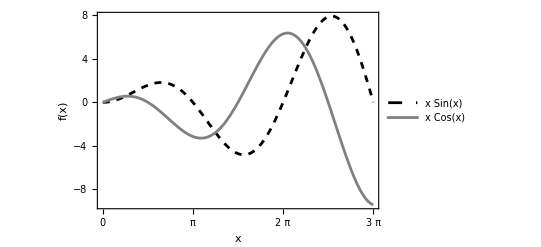

```mathematica
Plot[{x Sin[x],x Cos[x]},{x,0,3π},PlotStyle->{{Black,Dashed},Gray},
Frame->True,FrameStyle->{Black},
FrameLabel->{Style["x",16,FontFamily->"Times"],Style[Rotate["f(x)",-π/2],16,FontFamily->"Times"]},
FrameTicks->{{Automatic,None},{Table[n π,{n,0,3}](*{0,π,2π,3π}*),None}},
FrameTicksStyle->Directive[14,FontFamily->"Times"],
PlotLegends->Placed[LineLegend[{Style["x Sin(x)",14,FontFamily->"Times"],Style["x Cos(x)",14,FontFamily->"Times"]},LegendFunction->"Panel"],{0.2,0.8}],
PlotHighlighting->"Dropline",
ImageSize->400]
```

```mathematica
t=0;
A=1;
Manipulate[Plot[A Sin[x-t],{x,0,3π},PlotStyle->{Red},PlotRange->{-3,3},
Frame->True,FrameStyle->{Black},
FrameLabel->{Style["x",16,FontFamily->"Times"],Style[Rotate["f(x)",-π/2],16,FontFamily->"Times"]},
FrameTicksStyle->Directive[14,FontFamily->"Times"],
PlotLegends->"Expressions",
ImageSize->400],{t,0,10},{A,1,3}]
```

```mathematica
animation=AnimationVideo[Plot[Sin[x-t],{x,0,3π},PlotStyle->{Red},PlotRange->{-1.2,1.2},
Frame->True,FrameStyle->{Black},
FrameLabel->{Style["x",16,FontFamily->"Times"],Style[Rotate["f(x)",-π/2],16,FontFamily->"Times"]},
FrameTicks->{{Automatic,None}, {Table[j π,{j,0,3}],None}},
FrameTicksStyle->Directive[14,FontFamily->"Times"],
PlotLegends->"Expressions",
ImageSize->400],{t,0,6π}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["wave.mov",animation]
```

wave.mov

## Plot3D

```mathematica
plot3d=Plot3D[(Cos[x^2+y^2]+y^2)/(x^2+y^2+2),{x,-π,π},{y,-π,π},PlotPoints->50,PlotTheme->"Detailed",PlotStyle->{Opacity[0.2]},Mesh->70,
AxesLabel->{Style["x",16,FontFamily->"Times"],Style["y",16,FontFamily->"Times"],None}]
```

-Graphics3D-

```mathematica
FindMinimum[(Cos[x^2+y^2]+y^2)/(x^2+y^2+2),{x,y}]
```

{-0.19833,{x→1.71521,y→-1.23611×10^-10}}

```mathematica
sol=Reap@FindMinimum[(Cos[x^2+y^2]+y^2)/(x^2+y^2+2),{{x,0.1},{y,2.3}},EvaluationMonitor:>{Sow[{x,y,(Cos[x^2+y^2]+y^2)/(x^2+y^2+2)}]}]
```

{{-0.19833,{x→1.71521,y→2.42615×10^-9}},{{{0.1,2.3,0.800599},{0.0990013,1.55169,0.37546},{0.148408,1.57773,0.372713},{2.21241,2.27585,0.363011},{0.520713,1.70366,0.367822},{1.74177,2.11666,0.505957},{2.13422,2.2494,0.351089},{2.11688,2.24354,0.35064},{2.29365,2.25447,0.362601},{2.16038,2.24623,0.348911},{3.06448,1.32601,0.145365},{3.03982,1.10462,0.0570165},{1.79322,-0.422269,-0.146463},{0.700528,-0.151304,0.355604},{1.67076,-0.391901,-0.16727},{1.77415,0.0969535,-0.192066},{1.70553,-0.0326873,-0.19801},{1.71503,-0.00500006,-0.198325},{1.71541,-0.000243159,-0.19833},{1.71524,-0.0000141825,-0.19833},{1.71521,2.07861×10^-7,-0.19833},{1.71521,2.42615×10^-9,-0.19833}}}}

```mathematica
Show[plot3d,ListLinePlot3D[sol[[2,1]],PlotStyle->{PointSize[1/300],Thin,Red},Mesh->All],ImageSize->500]
```

-Graphics3D-

```mathematica
min={x,y}/.sol[[1,2]]
```

{1.71521,2.42615×10^-9}

```mathematica
Show[plot3d,ParametricPlot3D[{π,y,(Cos[x^2+y^2]+y^2)/(x^2+y^2+2)}/.{x->min[[1]]},{y,-π,π},PlotStyle->Red],
ParametricPlot3D[{x,-π,(Cos[x^2+y^2]+y^2)/(x^2+y^2+2)}/.{y->min[[2]]},{x,-π,π},PlotStyle->Red],ImageSize->500,ViewPoint->{π,-5,2}]
```

-Graphics3D-

## ContourPlot

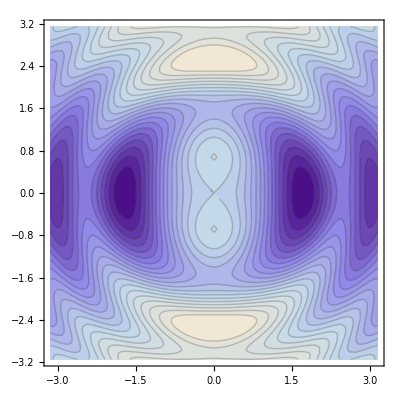

```mathematica
contourplot=ContourPlot[(Cos[x^2+y^2]+y^2)/(x^2+y^2+2),{x,-π,π},{y,-π,π},Contours->20,PlotTheme->"Classic",ContourStyle->{Opacity[0.2]}]
```

```mathematica
points={};
FindMinimum[(Cos[x^2+y^2]+y^2)/(x^2+y^2+2),{{x,0.1},{y,2.3}},EvaluationMonitor:>{AppendTo[points,{x,y}];Pause[0.25]}]
```

{-0.19833,{x→1.71521,y→2.42615×10^-9}}

```mathematica
Dynamic@Show[contourplot,ListLinePlot[points,PlotStyle->{Red,AbsoluteThickness[1]},PlotMarkers->{"×",16}]]
```